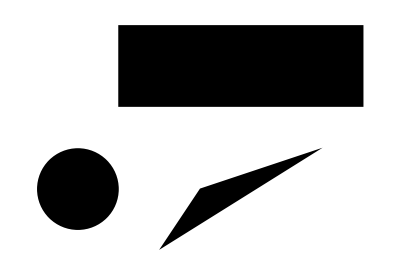

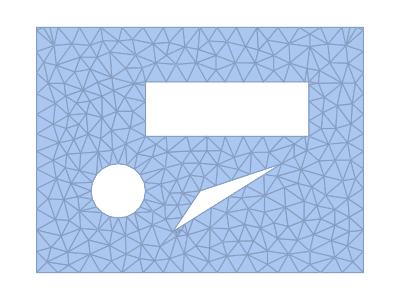

544

-Graphics-

83

```mathematica
Geometry={Disk[],Rectangle[{1,2},{7,4}],Triangle[{{3,0},{6,1},{2,-1.5}}]};

Graphics[Geometry]

DiscretizeRegion[RegionDifference[Rectangle[{-3,-3},{9,6}],RegionUnion@@Geometry]]
MeshCellCount[%,2]

HighlightMesh[bMesh=BoundaryMesh[DiscretizeRegion[RegionUnion@@Geometry]],Labeled[0,"Index"]]
NEl=MeshCellCount[%,1]
```

```mathematica
GreenF[x_,x0_]:=-N[1/2/Pi Log[Norm[x-x0]]]
DGreenF[x_,x0_]:=-N[1/2/Pi/Norm[x-x0]]

BElts=MeshPrimitives[bMesh,1];
Knots=RegionCentroid/@BElts;


G=Table[If[i!=j,NIntegrate[GreenF[Knots[[i]],BElts[[j,1,1]]+t(BElts[[j,1,2]]-BElts[[j,1,1]])],{t,0,1}],0],{i,1,NEl},{j,1,NEl}];
G=Transpose[(RegionMeasure/@BElts)Transpose[G]]+DiagonalMatrix[Table[#/Pi (1-Log[#])&[RegionMeasure[BElts[[i]]]/2] ,{i,1,NEl}]];

H=Transpose[(RegionMeasure/@BElts )Transpose[Table[If[i!=j,NIntegrate[({-#[[2]],#[[1]]}/Norm[#]&[(BElts[[j,1,2]]-BElts[[j,1,1]])]).(#/Norm[#]&[BElts[[j,1,1]]+t(BElts[[j,1,2]]-BElts[[j,1,1]])-Knots[[i]]])DGreenF[Knots[[i]],BElts[[j,1,1]]+t(BElts[[j,1,2]]-BElts[[j,1,1]])],{t,0,1}],0],{i,1,NEl},{j,1,NEl}]]];
H=H+1/2IdentityMatrix[NEl];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

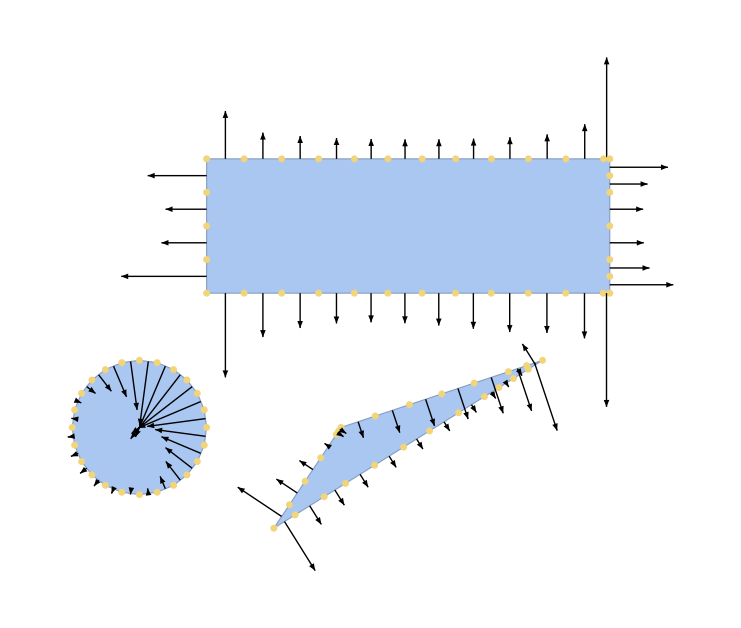

```mathematica
u0D=ConstantArray[1,Length[MeshCells[bMesh,2][[1,1]]]]~Join~ConstantArray[2,Length[MeshCells[bMesh,2][[2,1]]]]~Join~ConstantArray[3,Length[MeshCells[bMesh,2][[3,1]]]];
qSol=LinearSolve[G,H.u0D];

Show[HighlightMesh[bMesh,0],Graphics[{Arrowheads[.02],Table[Arrow[{Knots[[i]],Knots[[i]]-0.7(qSol[[i]]{#[[2]],-#[[1]]}/Norm[#]&[(BElts[[i,1,2]]-BElts[[i,1,1]])])}],{i,1,NEl}]}]]
```

Домашнее задание
1) Убедиться, что граничные элементы все направлены в одну сторону на контуре, т.е. нет двух элементов с концом или началом в одной точке.
2) Проверить решение семинарской задачи методом конечных элементов в Математике или Комсоле
3) Решить уравнение Лапласа в двумерном пространстве методом граничных элементов. Геометрия задачи - такая же, как и на семинаре (размеры указаны в метрах). Граничные условия:

Прямоугольник - металл, потенциал 1В
Диск - поле 2 В/м
Треугольник - металл, полный заряд 1нКл

4)* Придумать, как повысить быстродействие кода. Подробнее: http://blog.wolfram.com/2011/12/07/10-tips-for-writing-fast-mathematica-code/